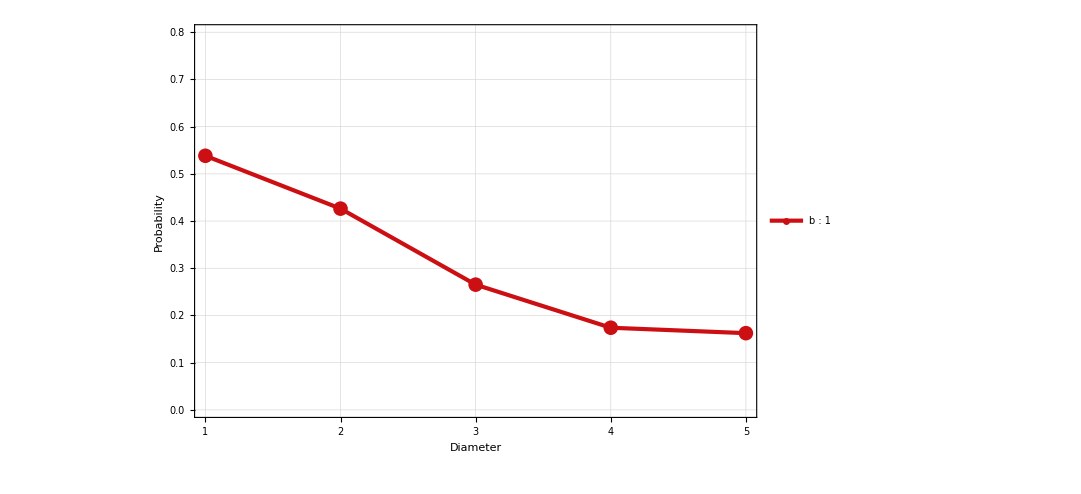

AVGconnectb1N10diameter10AllRsP02.eps

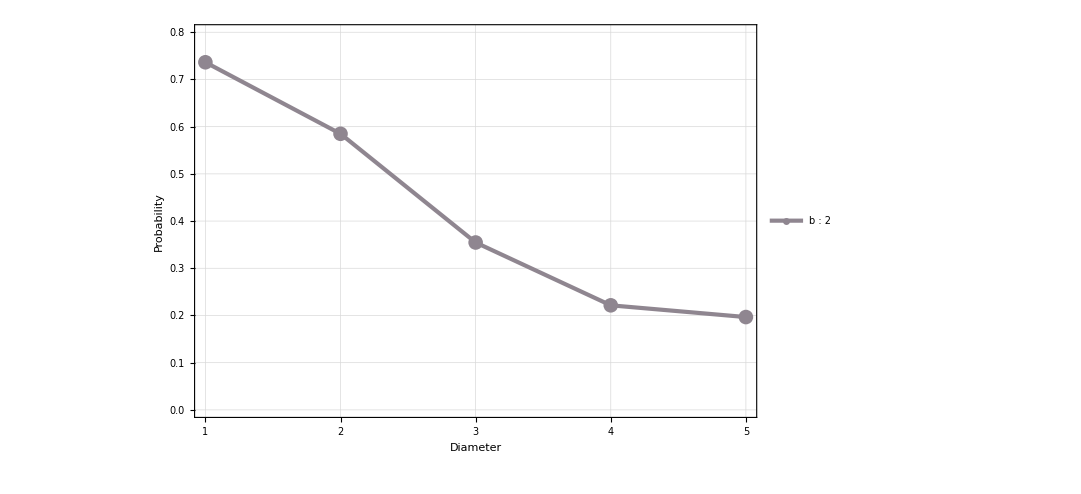

AVGconnectb2N10diameter10AllRsP02.eps

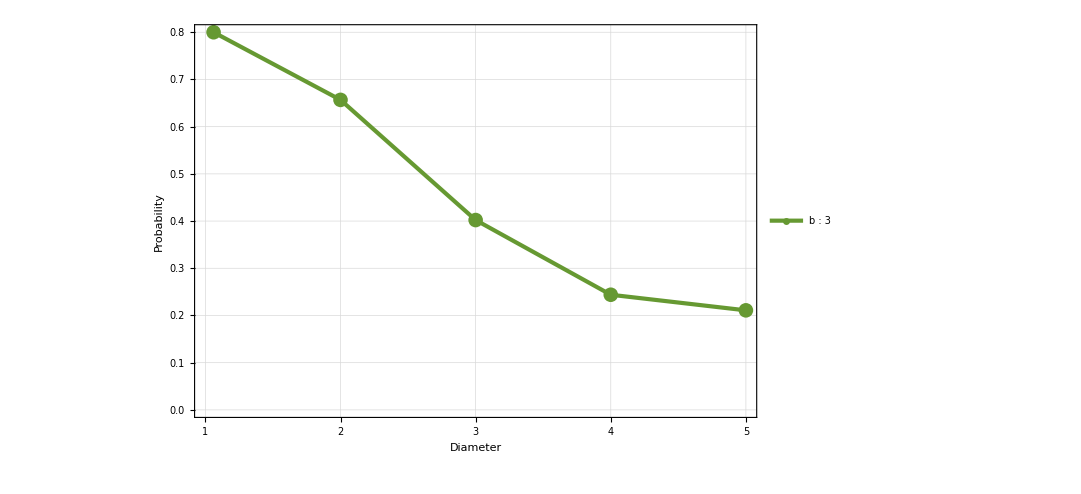

All20SET-AVGconnectb1b2b3N10diameter10AllRsP02.eps

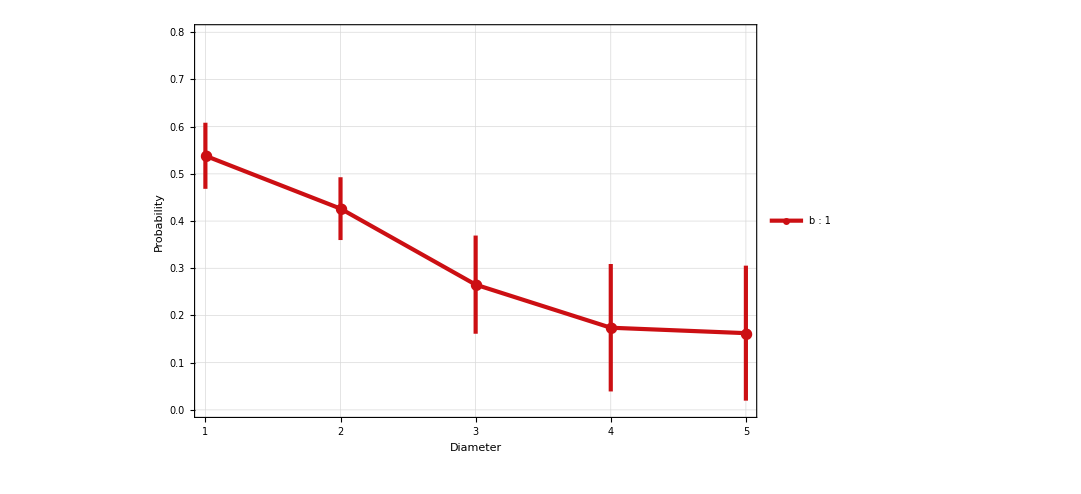

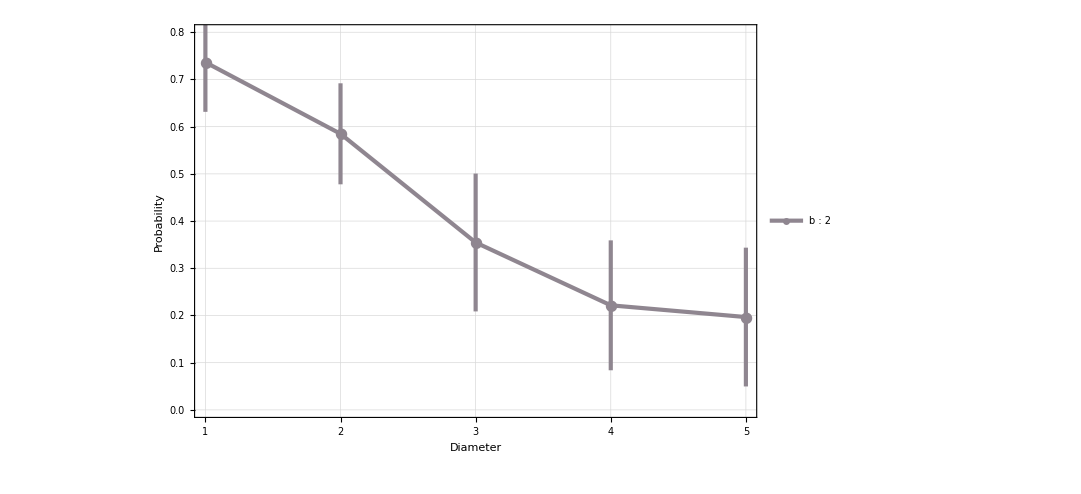

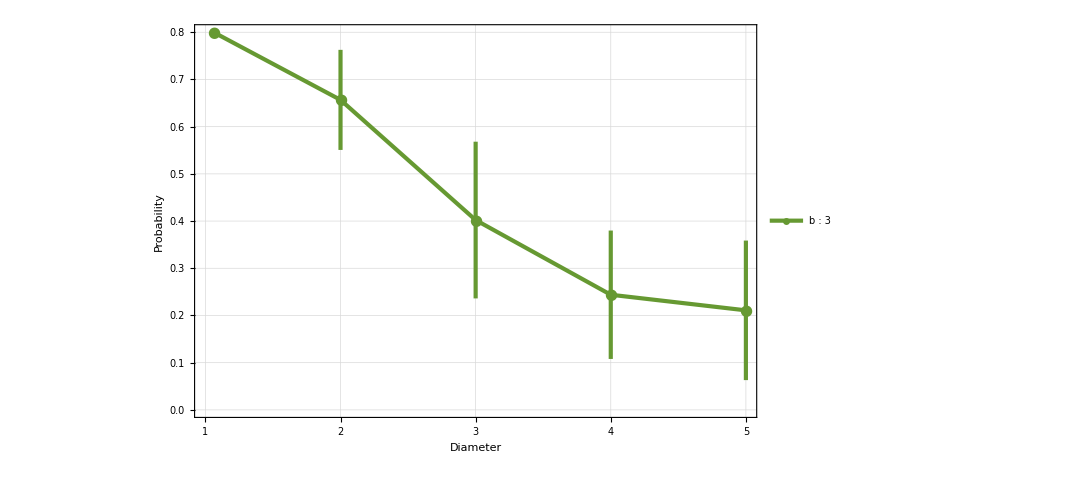

CI-AVGconnectb1b2b3N10diameter10AllRsP02.eps

myplot1-CI-AVGconnectb1b2b3N10diameter10AllRsP02.eps

myplot2-CI-AVGconnectb1b2b3N10diameter10AllRsP02.eps

myplot3-CI-AVGconnectb1b2b3N10diameter10AllRsP02.eps

```mathematica
(* plotting the result average probabilities against graph diameters *)
(* plotting the result average probabilities against graph diameters *)
(* b=1 *)
markers1={{●,15}};
AVGconnectb1N10diameter10AllRsP02=ListPlot[{{1,0.538311},{2,0.42632770935},{3,0.26530458525},{4,0.174034365},{5,0.162532898}},PlotMarkers->markers1,Frame->True ,FrameLabel->{Style["Diameter",Black,40],Style["Probability",Black,40]},PlotLegends->Placed[PointLegend[Style["b : 1",Black,40]&/@Range[4],LegendMarkers->markers1 ,LegendMarkerSize->50],{0.87,0.9}],FrameTicks->{{Automatic,None},{{1,2,3,4,5},None}},Joined->True,PlotStyle->(Directive[AbsoluteThickness[3],#]&/@ColorData[35,"ColorList"]),ImageSize->800,PlotRange->{{1,5},{0,0.8}},BaseStyle->{FontSize->45},GridLines->Automatic]

Export["AVGconnectb1N10diameter10AllRsP02.eps",Show[AVGconnectb1N10diameter10AllRsP02,PlotRange->{{1,5},{0,0.8}}]]


(* b=2 *)
markers1={{●,15}};
AVGconnectb2N10diameter10AllRsP02=ListPlot[{{1,0.736405},{2,0.584864022585},{3,0.35459216205},{4,0.2215082175},{5,0.1966499}},PlotMarkers->markers1,Frame->True ,FrameLabel->{Style["Diameter",Black,40],Style["Probability",Black,40]},PlotLegends->Placed[PointLegend[Style["b : 2",Black,40]&/@Range[4],LegendMarkers->markers1 ,LegendMarkerSize->50],{0.87,0.8}],FrameTicks->{{Automatic,None},{{1,2,3,4,5},None}},Joined->True,PlotStyle->(Directive[AbsoluteThickness[3],#]&/@ColorData[10,"ColorList"]),ImageSize->800,PlotRange->{{1,5},{0,0.8}},BaseStyle->{FontSize->45},GridLines->Automatic]

Export["AVGconnectb2N10diameter10AllRsP02.eps",Show[AVGconnectb2N10diameter10AllRsP02,PlotRange->{{1,5},{0,0.8}}]]


(* b=3 *)
markers1={{●,15}};
AVGconnectb3N10diameter10AllRsP02=ListPlot[{{1,0.809241},{2,0.6567137665},{3,0.402139972125},{4,0.2439068125},{5,0.210872495}},PlotMarkers->markers1,Frame->True ,FrameLabel->{Style["Diameter",Black,40],Style["Probability",Black,40]},PlotLegends->Placed[PointLegend[Style["b : 3",Black,40]&/@Range[4],LegendMarkers->markers1 ,LegendMarkerSize->50],{0.87,0.7}],FrameTicks->{{Automatic,None},{{1,2,3,4,5},None}},Joined->True,PlotStyle->(Directive[AbsoluteThickness[3],#]&/@ColorData[65,"ColorList"]),ImageSize->800,PlotRange->{{1,5},{0,0.8}},BaseStyle->{FontSize->45},GridLines->Automatic]

Export["All20SET-AVGconnectb1b2b3N10diameter10AllRsP02.eps",Show[AVGconnectb1N10diameter10AllRsP02,AVGconnectb2N10diameter10AllRsP02,AVGconnectb3N10diameter10AllRsP02,PlotRange->{{1,5},{0,0.8}}]]


(*************************************************************************************************************************************************************)
(* for b=1 *)
Needs["ErrorBarPlots`"]
myplot1=ErrorListPlot[{{{1,0.538311},ErrorBar[0.07]},{{2,0.42632770935},ErrorBar[0.0665223]},{{3,0.26530458525},ErrorBar[0.104]},{{4,0.174034365},ErrorBar[0.135]},{{5,0.162532898},ErrorBar[0.143]}},PlotMarkers->markers1,Frame->True ,FrameLabel->{Style["Diameter",Black,40],Style["Probability",Black,40]},PlotLegends->Placed[PointLegend[Style["b : 1",Black,40]&/@Range[4],LegendMarkers->markers1 ,LegendMarkerSize->50],{0.87,0.9}],FrameTicks->{{Automatic,None},{{1,2,3,4,5},None}},Joined->True,PlotStyle->(Directive[AbsoluteThickness[3],#]&/@ColorData[35,"ColorList"]),ImageSize->800,PlotRange->{{1,5},{0,0.8}},BaseStyle->{FontSize->45},GridLines->Automatic]
(* for b=1 *)


(* for b=2 *)
Needs["ErrorBarPlots`"]
myplot2=ErrorListPlot[{{{1,0.736405},ErrorBar[0.105]},{{2,0.584864022585},ErrorBar[0.107]},{{3,0.35459216205},ErrorBar[0.146]},{{4,0.2215082175},ErrorBar[0.1376]},{{5,0.1966499},ErrorBar[0.147]}},PlotMarkers->markers1,Frame->True ,FrameLabel->{Style["Diameter",Black,40],Style["Probability",Black,40]},PlotLegends->Placed[PointLegend[Style["b : 2",Black,40]&/@Range[4],LegendMarkers->markers1 ,LegendMarkerSize->50],{0.87,0.8}],FrameTicks->{{Automatic,None},{{1,2,3,4,5},None}},Joined->True,PlotStyle->(Directive[AbsoluteThickness[3],#]&/@ColorData[10,"ColorList"]),ImageSize->800,PlotRange->{{1,5},{0,0.8}},BaseStyle->{FontSize->45},GridLines->Automatic]
(* for b=2 *)


(* for b=3 *)
Needs["ErrorBarPlots`"]
myplot3=ErrorListPlot[{{{1,0.809241},ErrorBar[0.124]},{{2,0.6567137665},ErrorBar[0.106]},{{3,0.402139972125},ErrorBar[0.166]},{{4,0.2439068125},ErrorBar[0.136]},{{5,0.210872495},ErrorBar[0.1478]}},PlotMarkers->markers1,Frame->True ,FrameLabel->{Style["Diameter",Black,40],Style["Probability",Black,40]},PlotLegends->Placed[PointLegend[Style["b : 3",Black,40]&/@Range[4],LegendMarkers->markers1 ,LegendMarkerSize->50],{0.87,0.8}],FrameTicks->{{Automatic,None},{{1,2,3,4,5},None}},Joined->True,PlotStyle->(Directive[AbsoluteThickness[3],#]&/@ColorData[65,"ColorList"]),ImageSize->800,PlotRange->{{1,5},{0,0.8}},BaseStyle->{FontSize->45},GridLines->Automatic]
(* for b=3 *)

Export["CI-AVGconnectb1b2b3N10diameter10AllRsP02.eps",Show[myplot1,myplot3,PlotRange->{{1,5},{0,0.8}}]]
Export["myplot1-CI-AVGconnectb1b2b3N10diameter10AllRsP02.eps",Show[myplot1,PlotRange->{{1,5},{0,0.8}}]]
Export["myplot2-CI-AVGconnectb1b2b3N10diameter10AllRsP02.eps",Show[myplot2,PlotRange->{{1,5},{0,0.8}}]]
Export["myplot3-CI-AVGconnectb1b2b3N10diameter10AllRsP02.eps",Show[myplot3,PlotRange->{{1,5},{0,0.8}}]]
```